# Numerical implementation of the Z function

This implementation uses the representation in terms of error functions for small argument |z|<M and asymptotic expansion for argument |z| > M. Now M=4. 
Note: The choice of s in the asymptotic expansion is different from that given in the plasma formulary (their sigma).  Use of their sigma clearly doesn't work for example when Re[z] =0.  Then sigma must be 0 whereas their forumlua would have sigma=1.

### Z function module

```mathematica
Zfun[z0_]:=Module[{M=4.,s,y,q,z2},
z=N[z0];
If[Abs[z]<M,

1.772453851*I* E^(-z^2)(1+ Erf[I z]),	(* error function form  *)
	
	y=Im[z];	(* asymptotic expansion *)
	Which[y==0.,s=1,  y>0,s=0,   y<0,s=2];
	z2=z^2;
	q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
	1.772453851*I*s*E^(-z2)-q		(* end of asymptotic expansion *)
]	(* end if  *)
]	(* end module *)
```

## Testing of Zfun

```mathematica
Zfun[1+I]
```

-0.369058+0.540145 ⅈ

```mathematica
x={0,.1,1,2,5};
y={0.,.1,2,5};
TableForm[Table[Zfun[x[[i]]+y[[j]]*I],{i,1,5},{j,1,4}]]
```

0.+1.77245 ⅈ | 0.+1.58893 ⅈ | 0.+0.452677 ⅈ | 0.+0.196219 ⅈ
-0.198672+1.75482 ⅈ | -0.167198+1.57479 ⅈ | -0.0189018+0.451937 ⅈ | -0.00377991+0.196148 ⅈ
-1.07616+0.652049 ⅈ | -0.954564+0.661427 ⅈ | -0.164834+0.387268 ⅈ | -0.0365201+0.189294 ⅈ
-0.602681+0.0324636 ⅈ | -0.587715+0.0712551 ⅈ | -0.23251+0.262239 ⅈ | -0.0662039+0.171038 ⅈ
-0.204267+2.46157×10^-11 ⅈ | -0.204176+0.00426596 ⅈ | -0.173678+0.0720393 ⅈ | -0.0989716+0.100969 ⅈ

Test timing for 100 evaluations

```mathematica
Table[Zfun[.1*i*E^(.1*I*i)],{i,0,100}];
```

Time was 8.4 sec

### Plot for real argument

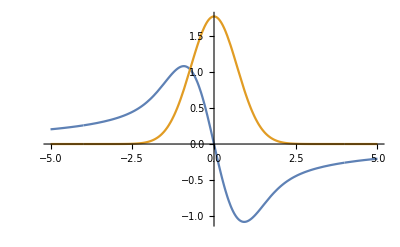

```mathematica
Plot[{Re[Zfun[x]],Im[Zfun[x]]},{x,-5,5},PlotRange->All]
```

## Testing of individual parts

### Erf form

```mathematica
Zf[z_]:=1.772453851*I* E^(-z^2)(1+ Erf[I z])//N
```

```mathematica
Zf[.1*I]
```

0.+1.58893 ⅈ

```mathematica
TableForm[Table[Zf[x[[i]]+y[[j]]*I],{i,1,5},{j,1,4}]]
```

0.+1.77245 ⅈ | 0.+1.58893 ⅈ | 0.+0.452677 ⅈ | 0.+0.196216 ⅈ
-0.198672+1.75482 ⅈ | -0.167198+1.57479 ⅈ | -0.0189018+0.451937 ⅈ | -0.00377898+0.196148 ⅈ
-1.07616+0.652049 ⅈ | -0.954564+0.661427 ⅈ | -0.164834+0.387268 ⅈ | -0.0365178+0.189297 ⅈ
-0.602681+0.0324636 ⅈ | -0.587715+0.0712551 ⅈ | -0.23251+0.262239 ⅈ | -0.0662041+0.171038 ⅈ
-0.204268+2.46157×10^-11 ⅈ | -0.204177+0.00426614 ⅈ | -0.173678+0.072039 ⅈ | -0.0989716+0.100969 ⅈ

These agree to printed accuracy with the Z function tables

### Check Symmetry

```mathematica
fsym[z_]:=(Zfun[Conjugate[z]]+Conjugate[Zfun[-z]])/Abs[Zfun[Conjugate[z]]]
```

```mathematica
TableForm[Table[fsym[i+j*I],{i,0,6,2},{j,-2,4,2}]]
```

0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ

```mathematica
fsym[z_]:=(Zf[Conjugate[z]]+Conjugate[Zf[-z]])/Abs[Zf[Conjugate[z]]]
TableForm[Table[fsym[i+j*I],{i,0,6,2},{j,-2,4,2}]]
```

0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ

### Asymptotic expansion

```mathematica
ZAsymp[z_]:=Module[{s,a,y,q,z2},
			a=Abs[Re[z]];
			y=Im[z];
			Which[y==0.,s=1,  y>0,s=0,   y<0,s=2];
			z2=z^2;
			q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
			N[1.772453851*I*s*E^(-z2)-q]
			]
```

```mathematica
TableForm[Table[ZAsymp[x[[i]]+y[[j]]*I],{i,2,5},{j,2,4}]]
```

-2.06241×10^8+2.03897×10^8 ⅈ | -0.0219314+0.457526 ⅈ | -0.00377991+0.196148 ⅈ
-7.40646+6.66096 ⅈ | -0.162507+0.38714 ⅈ | -0.0365201+0.189294 ⅈ
-0.607947+0.0504765 ⅈ | -0.232761+0.26218 ⅈ | -0.0662039+0.171038 ⅈ
-0.204176+0.00426596 ⅈ | -0.173678+0.0720393 ⅈ | -0.0989716+0.100969 ⅈ

This also checks with Z function table

Check Symmetry

```mathematica
fsym[z_]:=(ZAsymp[Conjugate[z]]+Conjugate[ZAsymp[-z]])/Abs[ZAsymp[Conjugate[z]]]
```

```mathematica
TableForm[Table[fsym[i+j*I],{i,-4,8,.51},{j,-5,5,2.5}]]
```

0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ

### Compare Erf form with asymptotic expansion

### Real argument

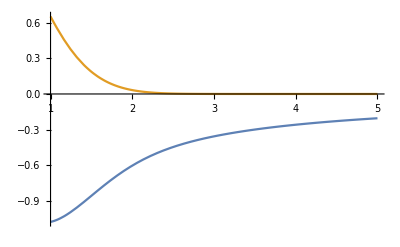

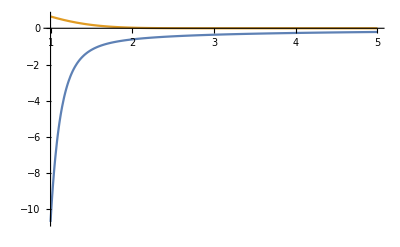

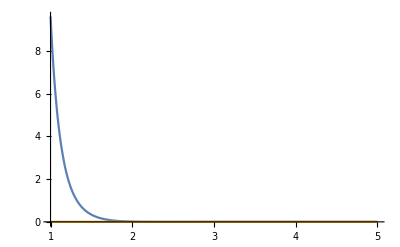

```mathematica
Plot[{Re[Zf[x]],Im[Zf[x]]},{x,1,5},PlotRange->All]
Plot[{Re[ZAsymp[x]],Im[ZAsymp[x]]},{x,1,5},PlotRange->All]
Plot[{Re[Zf[x]-ZAsymp[x]],Im[Zf[x]-ZAsymp[x]]},{x,1,5},PlotRange->All]
```

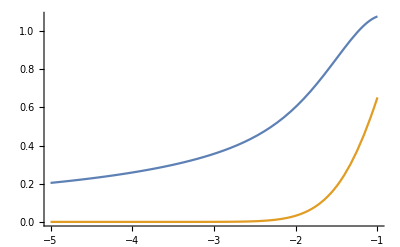

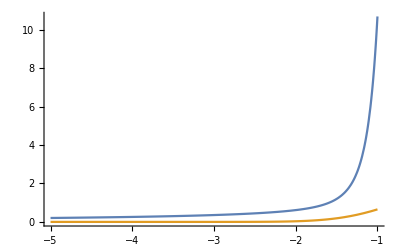

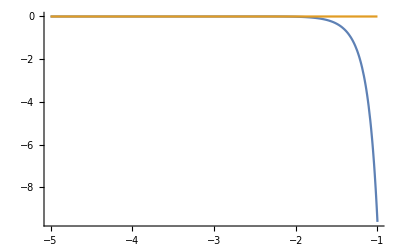

```mathematica
Plot[{Re[Zf[x]],Im[Zf[x]]},{x,-5,-1},PlotRange->All]
Plot[{Re[ZAsymp[x]],Im[ZAsymp[x]]},{x,-5,-1},PlotRange->All]
Plot[{Re[Zf[x]-ZAsymp[x]],Im[Zf[x]-ZAsymp[x]]},{x,-5,-1},PlotRange->All]
```

### Complex argument

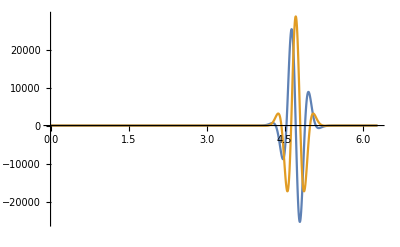

-Graphics-

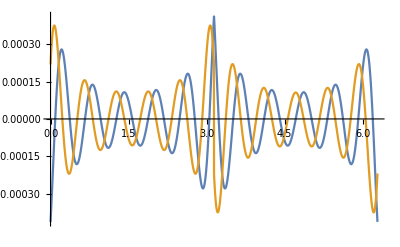

```mathematica
r=3.;
Plot[{Re[Zf[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
```

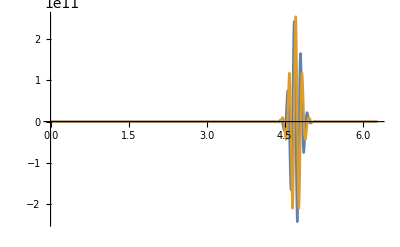

-Graphics-

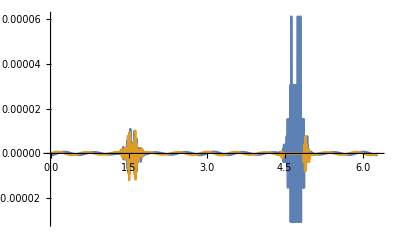

```mathematica
r=5.;
Plot[{Re[Zf[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
```

### Which raises the question : Does the Erf form have the wiggles at about 1.5 or not?

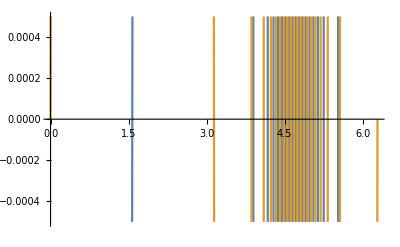

```mathematica
r=5.;
Plot[{Re[Zf[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange->{-.0005, .0005}]
```

### Yes, it does . Does my form of the asymptotic expansion have them?

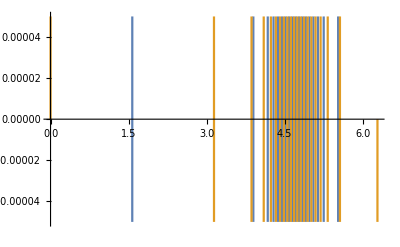

```mathematica
r=5.;
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange->{-.00005, .00005}]
```

### Yes, it does . So how well do they agree on the wiggles?

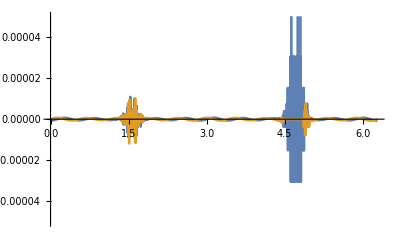

```mathematica
r=5.;
Plot[{Re[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]],Im[Zf[r*Exp[ⅈ theta]]-ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange->{-.00005, .00005}]
```

### They agree very well. What happens if we use the choice of s in the asymptotic expansion given in the NRL formulary?

```mathematica
ZAsymp2[z_Complex]:=Module[{s,a,y,q,z2},
			a=Abs[Re[z]];
			y=Im[z];
			Which[y>1/a,s=0,  Abs[y]<1/a,s=1,   y<-1/a,s=2];
			z2=z^2;
			q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
			N[1.772453851*I*s*E^(-z2)-q]
			]
```

-Graphics-

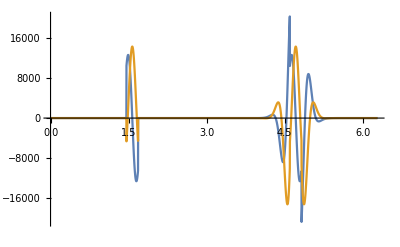

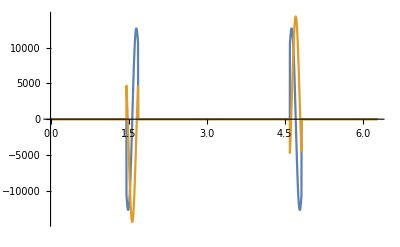

```mathematica
r=3.;
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp2[r*Exp[ⅈ theta]]],Im[ZAsymp2[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]-ZAsymp2[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]-ZAsymp2[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
```

-Graphics-

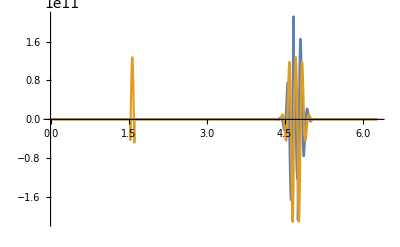

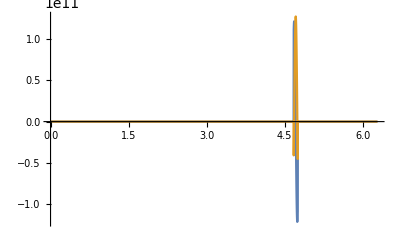

```mathematica
r=5.;
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp2[r*Exp[ⅈ theta]]],Im[ZAsymp2[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
Plot[{Re[ZAsymp[r*Exp[ⅈ theta]]-ZAsymp2[r*Exp[ⅈ theta]]],Im[ZAsymp[r*Exp[ⅈ theta]]-ZAsymp2[r*Exp[ⅈ theta]]]},{theta,0.,2 π},PlotRange→All]
```

## Set transition to asymptotics small, M=1.5 and look at break

```mathematica
Zfun[z0_]:=Module[{M=1.5,s,y,q,z2},
z=N[z0];
If[Abs[z]<M,

1.772453851*I* E^(-z^2)(1+ Erf[I z]),	(* error function form  *)
	
	y=Im[z];	(* asymptotic expansion *)
	Which[y==0.,s=1,  y>0,s=0,   y<0,s=2];
	z2=z^2;
	q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
	1.772453851*I*s*E^(-z2)-q		(* end of asymptotic expansion *)
]	(* end if  *)
]	(* end module *)
```

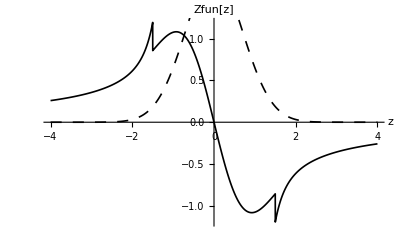

```mathematica
zf=Table[{z,Zfun[z]},{z,-4,4,.001}];
ComplexVectorListPlot[zf,"z","Zfun[z]", PlotRange->All]
```

### M = 2.

```mathematica
Zfun[z0_]:=Module[{M=2.,s,y,q,z2},
z=N[z0];
If[Abs[z]<M,

1.772453851*I* E^(-z^2)(1+ Erf[I z]),	(* error function form  *)
	
	y=Im[z];	(* asymptotic expansion *)
	Which[y==0.,s=1,  y>0,s=0,   y<0,s=2];
	z2=z^2;
	q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
	1.772453851*I*s*E^(-z2)-q		(* end of asymptotic expansion *)
]	(* end if  *)
]	(* end module *)
```

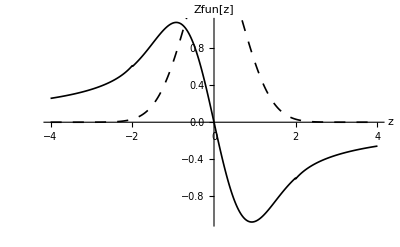

```mathematica
zf=Table[{z,Zfun[z]},{z,-4,4,.01}];
ComplexVectorListPlot[zf,"z","Zfun[z]", PlotRange->All]
```

## Run case to compare with fortran zfun ()

```mathematica
xt=Table[i,{i,-10,10}];
yt=Table[i,{i,-1,1}];
TableForm[Table[Zfun[xt[[i]]+yt[[j]]*I],{i,1,21},{j,1,3}]];
Do[Print["i = ", i, "  j = ", j,"   Zfun = ", Zfun[i+j*I]],{j,-1, 1},{i,-10, 10}]
```

i = -10  j = -1   Zfun = 0.0994872-0.0100497 ⅈ

i = -9  j = -1   Zfun = 0.110403-0.0124213 ⅈ

i = -8  j = -1   Zfun = 0.123984-0.0157459 ⅈ

i = -7  j = -1   Zfun = 0.141321-0.0206136 ⅈ

i = -6  j = -1   Zfun = 0.16418-0.0281556 ⅈ

i = -5  j = -1   Zfun = 0.19556-0.0407715 ⅈ

i = -4  j = -1   Zfun = 0.240776-0.064306 ⅈ

i = -3  j = -1   Zfun = 0.308003-0.114739 ⅈ

i = -2  j = -1   Zfun = 0.256227-0.364477 ⅈ

i = -1  j = -1   Zfun = 3.59243-2.01535 ⅈ

i = 0  j = -1   Zfun = 0.+8.87819 ⅈ

i = 1  j = -1   Zfun = -3.59243-2.01535 ⅈ

i = 2  j = -1   Zfun = -0.256227-0.364477 ⅈ

i = 3  j = -1   Zfun = -0.308003-0.114739 ⅈ

i = 4  j = -1   Zfun = -0.240776-0.064306 ⅈ

i = 5  j = -1   Zfun = -0.19556-0.0407715 ⅈ

i = 6  j = -1   Zfun = -0.16418-0.0281556 ⅈ

i = 7  j = -1   Zfun = -0.141321-0.0206136 ⅈ

i = 8  j = -1   Zfun = -0.123984-0.0157459 ⅈ

i = 9  j = -1   Zfun = -0.110403-0.0124213 ⅈ

i = 10  j = -1   Zfun = -0.0994872-0.0100497 ⅈ

i = -10  j = 0   Zfun = 0.100508+6.59366×10^-44 ⅈ

i = -9  j = 0   Zfun = 0.11181+1.17685×10^-35 ⅈ

i = -8  j = 0   Zfun = 0.126+2.84268×10^-28 ⅈ

i = -7  j = 0   Zfun = 0.144362+9.29277×10^-22 ⅈ

i = -6  j = 0   Zfun = 0.169085+4.11125×10^-16 ⅈ

i = -5  j = 0   Zfun = 0.204267+2.46157×10^-11 ⅈ

i = -4  j = 0   Zfun = 0.258684+1.99463×10^-7 ⅈ

i = -3  j = 0   Zfun = 0.356129+0.000218738 ⅈ

i = -2  j = 0   Zfun = 0.613403+0.0324636 ⅈ

i = -1  j = 0   Zfun = 1.07616+0.652049 ⅈ

i = 0  j = 0   Zfun = 0.+1.77245 ⅈ

i = 1  j = 0   Zfun = -1.07616+0.652049 ⅈ

i = 2  j = 0   Zfun = -0.613403+0.0324636 ⅈ

i = 3  j = 0   Zfun = -0.356129+0.000218738 ⅈ

i = 4  j = 0   Zfun = -0.258684+1.99463×10^-7 ⅈ

i = 5  j = 0   Zfun = -0.204267+2.46157×10^-11 ⅈ

i = 6  j = 0   Zfun = -0.169085+4.11125×10^-16 ⅈ

i = 7  j = 0   Zfun = -0.144362+9.29277×10^-22 ⅈ

i = 8  j = 0   Zfun = -0.126+2.84268×10^-28 ⅈ

i = 9  j = 0   Zfun = -0.11181+1.17685×10^-35 ⅈ

i = 10  j = 0   Zfun = -0.100508+6.59366×10^-44 ⅈ

i = -10  j = 1   Zfun = 0.0994872+0.0100497 ⅈ

i = -9  j = 1   Zfun = 0.110403+0.0124213 ⅈ

i = -8  j = 1   Zfun = 0.123984+0.0157459 ⅈ

i = -7  j = 1   Zfun = 0.141321+0.0206136 ⅈ

i = -6  j = 1   Zfun = 0.16418+0.0281556 ⅈ

i = -5  j = 1   Zfun = 0.19556+0.0407715 ⅈ

i = -4  j = 1   Zfun = 0.240775+0.0643059 ⅈ

i = -3  j = 1   Zfun = 0.308335+0.115881 ⅈ

i = -2  j = 1   Zfun = 0.389796+0.249115 ⅈ

i = -1  j = 1   Zfun = 0.369058+0.540145 ⅈ

i = 0  j = 1   Zfun = 0.+0.757872 ⅈ

i = 1  j = 1   Zfun = -0.369058+0.540145 ⅈ

i = 2  j = 1   Zfun = -0.389796+0.249115 ⅈ

i = 3  j = 1   Zfun = -0.308335+0.115881 ⅈ

i = 4  j = 1   Zfun = -0.240775+0.0643059 ⅈ

i = 5  j = 1   Zfun = -0.19556+0.0407715 ⅈ

i = 6  j = 1   Zfun = -0.16418+0.0281556 ⅈ

i = 7  j = 1   Zfun = -0.141321+0.0206136 ⅈ

i = 8  j = 1   Zfun = -0.123984+0.0157459 ⅈ

i = 9  j = 1   Zfun = -0.110403+0.0124213 ⅈ

i = 10  j = 1   Zfun = -0.0994872+0.0100497 ⅈ

### Compare this to the fortan result for zfun0 (), for kx > 0

z =    -10.00000    - 1.00000  zfun0  =     9.94872078 E - 02   - 1.00497119 E - 02
z =     -9.00000    - 1.00000  zfun0  =     1.10403456 E - 01   - 1.24213258 E - 02
z =     -8.00000    - 1.00000  zfun0  =     1.23983875 E - 01   - 1.57458782 E - 02
z =     -7.00000    - 1.00000  zfun0  =     1.41321406 E - 01   - 2.06135754 E - 02
z =     -6.00000    - 1.00000  zfun0  =     1.64180189 E - 01   - 2.81556565 E - 02
z =     -5.00000    - 1.00000  zfun0  =     1.95559904 E - 01   - 4.07720059 E - 02
z =     -4.00000    - 1.00000  zfun0  =     2.40769416 E - 01   - 6.43073916 E - 02
z =     -3.00000    - 1.00000  zfun0  =     3.07929844 E - 01   - 1.14630915 E - 01
z =     -2.00000    - 1.00000  zfun0  =     2.60294497 E - 01   - 3.63930106 E - 01
z =     -1.00000    - 1.00000  zfun0  =     3.59243393 E + 00   - 2.01534724 E + 00
z =      0.00000    - 1.00000  zfun0  =     0.00000000 E + 00    8.87818623 E + 00
z =      1.00000    - 1.00000  zfun0  =    -3.59243393 E + 00   - 2.01534724 E + 00
z =      2.00000    - 1.00000  zfun0  =    -2.60294497 E - 01   - 3.63930106 E - 01
z =      3.00000    - 1.00000  zfun0  =    -3.07929844 E - 01   - 1.14630915 E - 01
z =      4.00000    - 1.00000  zfun0  =    -2.40769416 E - 01   - 6.43073916 E - 02
z =      5.00000    - 1.00000  zfun0  =    -1.95559904 E - 01   - 4.07720059 E - 02
z =      6.00000    - 1.00000  zfun0  =    -1.64180189 E - 01   - 2.81556565 E - 02
z =      7.00000    - 1.00000  zfun0  =    -1.41321406 E - 01   - 2.06135754 E - 02
z =      8.00000    - 1.00000  zfun0  =    -1.23983875 E - 01   - 1.57458782 E - 02
z =      9.00000    - 1.00000  zfun0  =    -1.10403456 E - 01   - 1.24213258 E - 02
z =     10.00000    - 1.00000  zfun0  =    -9.94872078 E - 02   - 1.00497119 E - 02
z =    -10.00000     0.00000  zfun0  =     1.00507706 E - 01    6.72623263 E - 44
z =     -9.00000     0.00000  zfun0  =     1.11810103 E - 01    1.17685215 E - 35
z =     -8.00000     0.00000  zfun0  =     1.26000404 E - 01    2.84268102 E - 28
z =     -7.00000     0.00000  zfun0  =     1.44361973 E - 01    9.29277339 E - 22
z =     -6.00000     0.00000  zfun0  =     1.69085383 E - 01    4.11124699 E - 16
z =     -5.00000     0.00000  zfun0  =     2.04268143 E - 01    2.46157400 E - 11
z =     -4.00000     0.00000  zfun0  =     2.58695990 E - 01    1.99463415 E - 07
z =     -3.00000     0.00000  zfun0  =     3.56541991 E - 01    2.18738191 E - 04
z =     -2.00000     0.00000  zfun0  =     6.02680504 E - 01    3.24636251 E - 02
z =     -1.00000     0.00000  zfun0  =     1.07615900 E + 00    6.52049363 E - 01
z =      0.00000     0.00000  zfun0  =    -0.00000000 E + 00    1.77245390 E + 00
z =      1.00000     0.00000  zfun0  =    -1.07615900 E + 00    6.52049363 E - 01
z =      2.00000     0.00000  zfun0  =    -6.02680504 E - 01    3.24636251 E - 02
z =      3.00000     0.00000  zfun0  =    -3.56541991 E - 01    2.18738191 E - 04
z =      4.00000     0.00000  zfun0  =    -2.58695990 E - 01    1.99463415 E - 07
z =      5.00000     0.00000  zfun0  =    -2.04268143 E - 01    2.46157400 E - 11
z =      6.00000     0.00000  zfun0  =    -1.69085383 E - 01    4.11124699 E - 16
z =      7.00000     0.00000  zfun0  =    -1.44361973 E - 01    9.29277339 E - 22
z =      8.00000     0.00000  zfun0  =    -1.26000404 E - 01    2.84268102 E - 28
z =      9.00000     0.00000  zfun0  =    -1.11810103 E - 01    1.17685215 E - 35
z =     10.00000     0.00000  zfun0  =    -1.00507706 E - 01    6.72623263 E - 44
z =    -10.00000     1.00000  zfun0  =     9.94872078 E - 02    1.00497119 E - 02
z =     -9.00000     1.00000  zfun0  =     1.10403456 E - 01    1.24213258 E - 02
z =     -8.00000     1.00000  zfun0  =     1.23983875 E - 01    1.57458782 E - 02
z =     -7.00000     1.00000  zfun0  =     1.41321406 E - 01    2.06135754 E - 02
z =     -6.00000     1.00000  zfun0  =     1.64180189 E - 01    2.81556565 E - 02
z =     -5.00000     1.00000  zfun0  =     1.95559904 E - 01    4.07720059 E - 02
z =     -4.00000     1.00000  zfun0  =     2.40768343 E - 01    6.43072352 E - 02
z =     -3.00000     1.00000  zfun0  =     3.08262140 E - 01    1.15772724 E - 01
z =     -2.00000     1.00000  zfun0  =     3.93863022 E - 01    2.48568162 E - 01
z =     -1.00000     1.00000  zfun0  =     3.69058460 E - 01    5.40145040 E - 01
z =      0.00000     1.00000  zfun0  =    -0.00000000 E + 00    7.57872522 E - 01
z =      1.00000     1.00000  zfun0  =    -3.69058460 E - 01    5.40145040 E - 01
z =      2.00000     1.00000  zfun0  =    -3.93863022 E - 01    2.48568162 E - 01
z =      3.00000     1.00000  zfun0  =    -3.08262140 E - 01    1.15772724 E - 01
z =      4.00000     1.00000  zfun0  =    -2.40768343 E - 01    6.43072352 E - 02
z =      5.00000     1.00000  zfun0  =    -1.95559904 E - 01    4.07720059 E - 02
z =      6.00000     1.00000  zfun0  =    -1.64180189 E - 01    2.81556565 E - 02
z =      7.00000     1.00000  zfun0  =    -1.41321406 E - 01    2.06135754 E - 02
z =      8.00000     1.00000  zfun0  =    -1.23983875 E - 01    1.57458782 E - 02
z =      9.00000     1.00000  zfun0  =    -1.10403456 E - 01    1.24213258 E - 02
z =     10.00000     1.00000  zfun0  =    -9.94872078 E - 02    1.00497119 E - 02

### This agrees very well but what if kz is taken as < 0?